## Gravito-scalar QNMs of Schwarzschild BHs in Dynamical Chern-Simons gravity Reference: Paolo Pani, “Advanced methods in Black-Hole Perturbation Theory” (2013)

#### Perturbation equations:

```mathematica
Clear[u1,u2];
ϵa=1;
F[r_]:=1-2M/r;
V1=F[r]((l(l+1))/r^2-(6M)/r^3);
V2=F[r]((l(l+1))/r^2+(2M)/r^3);
S1=4(2 α-1)(9 M^2+(l^2+l -4) M r +r^2(2-l-l^2+r^2 ω^2))/(r^3(6 M + ( l + 2 ) (l - 1) r ));
S2=0;
e1=F[r]^2 u1''[r]+F'[r]F[r]u1'[r]+(ω^2-V1)u1[r]-S1 u2[r]
e2=F[r]^2 u2''[r]+F'[r]F[r]u2'[r]+(ω^2-V2)u2[r]-S2 u1[r]
```

(-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u1[r]-(4 (-1+2 α) (9 M^2+(-4+l+l^2) M r+r^2 (2-l-l^2+r^2 ω^2)) u2[r])/(r^3 (6 M+(-1+l) (2+l) r))+(2 M (1-(2 M)/r) u1'[r])/r^2+(1-(2 M)/r)^2 u1''[r]

(-((2 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u2[r]+(2 M (1-(2 M)/r) u2'[r])/r^2+(1-(2 M)/r)^2 u2''[r]

#### Series at the horizon [arbitrary order]

```mathematica
Clear[u1,u2];

u1[r_]:=(r-2M)^bb G1[r];
u2[r_]:=(r-2M)^bb G2[r];
Es1=FullSimplify[(r^6 e1)/(-2 M+r)^bb];
Es2=FullSimplify[e2/(1/(r^9 β ω Gamma[-1+l])(-2 M+r)^bb)];
```

```mathematica
ORD=5;
G1[r_]:=Sum[u1h[i](r-2M)^i,{i,0,ORD+3}];
G2[r_]:=Sum[u2h[i](r-2M)^i,{i,0,ORD+3}];
ss=Series[{Es1,Es2}/.{bb->-2 ⅈ M ω},{r,2M,ORD+3}];
yh=Union[Table[u1h[i],{i,1,ORD}],Table[u2h[i],{i,1,ORD}]];
EQsh=Union[Table[Normal[Series[SeriesCoefficient[ss[[1]],i],{J,0,1}]]==0,{i,1,ORD}],Table[Normal[Series[SeriesCoefficient[ss[[2]],i],{J,0,1}]]==0,{i,1,ORD}]];
Length[yh]
Length[EQsh]
seriesH=Solve[EQsh,yh][[1]];

Clear[u1,u2,G1,G2]
```

10

10

```mathematica
Solve[bb^2 M^2+4 M^4 ω^2==0,bb]
```

{{bb→-2 ⅈ M ω},{bb→2 ⅈ M ω}}

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["seriesH.mx",{seriesH,ORD}];*)
```

#### Series at infinity [arbitrary order]

```mathematica
u1[r_]:=Exp[kk r] r^n G1[r];
u2[r_]:=Exp[kk r] r^n G2[r];
Es1=FullSimplify[e1/(ⅇ^(kk r) r^n)]
Es2=FullSimplify[e2/(ⅇ^(kk r) r^n)]
```

(-((2 M-r) (6 M-l (1+l) r))/r^4+ω^2) G1[r]-(4 (-1+2 α) (9 M^2+(-4+l+l^2) M r-(-2+l+l^2) r^2+r^4 ω^2) G2[r])/(r^3 (6 M+(-2+l+l^2) r))+(2 M (-2 M+r) ((n+kk r) G1[r]+r G1'[r]))/r^4+((-2 M+r)^2 (((-1+n) n+2 kk n r+kk^2 r^2) G1[r]+r (2 (n+kk r) G1'[r]+r G1''[r])))/r^4

1/r^4(((2 M-r) (r (l+l^2+n-n^2-2 kk n r-kk^2 r^2)+2 M (1+n^2+2 n (-1+kk r)+kk r (-1+kk r)))+r^4 ω^2) G2[r]+r (-2 M+r) (2 (M (1-2 n-2 kk r)+r (n+kk r)) G2'[r]+r (-2 M+r) G2''[r]))

```mathematica
ORDinf=2;
G1[r_]:=Sum[u1inf[i]/r^i,{i,0,ORDinf+3}];
G2[r_]:=Sum[u2inf[i]/r^i,{i,0,ORDinf+4}]
ruleINF={kk^2->-ω^2,n->-(2 M ω^2)/kk};
ss=Series[{Es1,Es2},{r,∞,ORDinf+3}]/.ruleINF;
yinf=Union[Table[u1inf[i],{i,1,ORDinf+1}],Table[u2inf[i],{i,1,ORDinf+2}]];
EQsinf=Union[Table[SeriesCoefficient[ss[[1]],i]==0,{i,2,ORDinf+2}],Table[SeriesCoefficient[ss[[2]],i]==0,{i,2,ORDinf+3}]];
Length[yinf]
Length[EQsinf]
seriesINF=Solve[EQsinf,yinf][[1]]//Simplify;
(* seriesINF are rules of the form u1inf[i], u2inf[i] -> u1inf[0], u2inf[0]*)
seriesINF /. {u1inf[0]->0,u2inf[0]->0}
Clear[u1,u2,G1,G2]
```

7

7

{u1inf[1]→0,u1inf[2]→0,u1inf[3]→0,u2inf[1]→0,u2inf[2]→0,u2inf[3]→0,u2inf[4]→0}

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["seriesINF.mx",{seriesINF,ORDinf}];*)
```

#### Higher order BCs at infinity

```mathematica
(*<<"seriesINF.mx";*)
ORDinf2=(ORDinf+1);
(*ORDinf2=0;*)
y1=(Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+ (Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y1p=D[y1,r];
y2= (Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+(Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y2p=D[y2,r];
solBC=Solve[{y1==Y1,y1p==Y1p,y2==Y2,y2p==Y2p},{B1,C1,B2,C2}];
Length[solBC]
solBC=solBC[[1]];
```

1

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["solBC.mx",{solBC}];*)
```

```mathematica
Length[solBC]
```

4

#### Integrator:

```mathematica
SetDirectory[NotebookDirectory[]];
INT[ω0_,α0_,u10_,u20_,l0_,EPS_,INF_]:=(
ruleP={AccuracyGoal->80,PrecisionGoal->12,MaxSteps->10^5};
ruleP={};

param={M->1,l->l0,ω->ω0,u1h[0]->u10,u2h[0]->u20,β->1,α->α0};
rhn=2M(1+EPS)/.param;
rinf=INF;

(*<<"seriesH.mx";*)
u1g=(r-2M)^(-2I ω M)Sum[u1h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH];
u2g=(r-2M)^(-2I ω M)Sum[u2h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH];
EQs={e1==0, e2==0}//.param;
BCs={u1[rhn]==u1g/.r->rhn,u1'[rhn]==D[u1g,r]/.r->rhn,u2[rhn]==u2g/.r->rhn,u2'[rhn]==D[u2g,r]/.r->rhn};
sol=NDSolve[Union[EQs,BCs],{u1,u2},{r,rhn,rinf},ruleP];
u1n=u1[r]/.sol[[1]];
u2n=u2[r]/.sol[[1]];

);
```

```mathematica
INT[0.1-0.1I,1,1,1,2,10^-4,10^2];
{u1n,u2n}/.r->rinf
```

{6.37162×10^8+5.12121×10^8 ⅈ,-6.80914×10^7+1.68647×10^7 ⅈ}

```mathematica
INT[0.1-0.1I,1/2,0,1,2,10^-4,10^2];
(* This only excites the scalar field *)
{u1n,u2n}/.r->rinf
```

{-3.65669×10^-14-4.8832×10^-14 ⅈ,-6.80914×10^7+1.68647×10^7 ⅈ}

```mathematica
INT[0.1-0.1I,1/2,1,0,2,10^-4,10^2];
(* This only excites the metric field *)
{u1n,u2n}/.r->rinf
```

{-9.86946×10^6+3.53856×10^6 ⅈ,0.+0. ⅈ}

#### DETERMINANT

```mathematica
SetDirectory[NotebookDirectory[]];
LINCOMB[ω0_,α0_,l0_,EPS_,INF_]:=(

(*<<"polar_solBC.mx";*)


INT[ω0,α0,1,0,l0,EPS,INF];
u110=u1n;
u210=u2n;
u110p=D[u1n,r];
u210p=D[u2n,r];
rule10=Union[solBC,param,{k->I ω,Y1->u110,Y1p->u110p,Y2->u210,Y2p->u210p,r->rinf}];
B110=B1//.rule10;
C110=C1//.rule10;
B210=B2//.rule10;
C210=C2//.rule10;
INT[ω0,α0,0,1,l0,EPS,INF];
u101=u1n;
u201=u2n;
u101p=D[u1n,r];
u201p=D[u2n,r];
rule01=Union[solBC,param,{k->I ω,Y1->u101,Y1p->u101p,Y2->u201,Y2p->u201p,r->rinf}];
B101=B1//.rule01;
C101=C1//.rule01;
B201=B2//.rule01;
C201=C2//.rule01;
(************)
BB=B110 B201-B101 B210;
CC=C110 C201-C101 C210;
(*Print[{"ω0 =" , ω0, "BB = ",BB}];*)
{BB}(*BB for QNMs, CC for quasi-bound states*)
)
```

```mathematica
LINCOMB[0.1+0.0001I,0.5,2,10^-6,10^2]
```

371705.-1.94423×10^6 ⅈ

{371705.-1.94423×10^6 ⅈ}

```mathematica
LINCOMB[0.1+0.0001I,1,2,10^-6,10^2]
```

371705.-1.94424×10^6 ⅈ

{371705.-1.94424×10^6 ⅈ}

```mathematica
LINCOMB[0.1+0.0001I,0,2,10^-6,10^2]
```

371705.-1.94424×10^6 ⅈ

{371705.-1.94424×10^6 ⅈ}

#### Find root:

```mathematica
(**************************************************)
ωguess=0.37-0.09 ⅈ;(*scal*)
f4[y_?NumericQ]:=LINCOMB[y,0.5,2,1 10^-3,100][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
Abs[f4[y0n]]
(* Finds 0.35608598419017534 - 0.07190616786549635 ⅈ *)
```

0.356086-0.0719062 ⅈ

{ω0 =,0.356086-0.0719062 ⅈ,BB = ,7.1566×10^-9+3.46433×10^-9 ⅈ}

7.95101×10^-9

```mathematica
(**************************************************)
ωguess=0.35608598419017534 - 0.07190616786549635 I;(*scal*)
f4[y_?NumericQ]:=LINCOMB[y,0,2,1 10^-3,100][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess},AccuracyGoal->2,PrecisionGoal->12][[1]]
Abs[f4[y0n]]
(* returns 0.35608598418957904-0.07190616786578917 ⅈ *)
```

0.356086-0.0719062 ⅈ

{ω0 =,0.356086-0.0719062 ⅈ,BB = ,2.15433×10^-9+5.93586×10^-9 ⅈ}

6.31471×10^-9

```mathematica
(0.35608598419017534-0.07190616786549635 ⅈ) - (0.35608598418957904-0.07190616786578917 ⅈ)
```

5.96301×10^-13+2.92821×10^-13 ⅈ

### Tracking

```mathematica
xi=-1;
xf=1;
dim=20;
dx=(xf-xi)/dim;
TT=Table[Null,{dim}];
xx=xi;
(****)
α00=xi;

ωguess=0.35608598419017534-0.07190616786549635 ⅈ;(*l=2*)



(****)
Monitor[For[j=1,j<dim+1,{
(* LINCOMB[ω0_,α0_,l0_,EPS_,INF_] *)
f4[y_?NumericQ]:=LINCOMB[y,xx,2,10^-3,100][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->12,PrecisionGoal->12*)][[1]];
check=Abs[f4[y0n]];
TT[[j]]={N[xx],y0n,check};
ωguess=y0n;
xx=xx+dx;
j++;
}],{j,N[xx],y0n,check}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

$Aborted

```mathematica
TR=Table[{TT[[i]][[1]],Re[TT[[i]][[2]]]},{i,1,Length[TT]}];
TI=Table[{TT[[i]][[1]],Im[TT[[i]][[2]]]},{i,1,Length[TT]}];
```

```mathematica
TR1=TR;
TI1=TI;
```

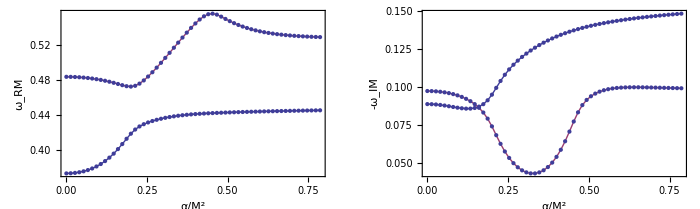

```mathematica
(***)
p1=ListPlot[{TR1,TR2},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","ω_RM"},Axes->False];
p2=ListPlot[{Abs[TI1],Abs[TI2]},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","-ω_IM"},PlotRange->All,Axes->False];
GraphicsGrid[{{p1,p2}},ImageSize->700]
```

### Higher-l

```mathematica
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)
ωguess=1.40974-0.0955096 I;(*l=7*)
ωguess=1.9916474515518394-0.287911944390142 I;(*l=10*)
ωguess=2-0.3 I;(*l=10*)
(*ωguess=0.7337751980725775-0.127070807565408 ⅈ;(*scal*)*)
(**************************************************)

f4[y_?NumericQ]:=LINCOMB[y,0,10,1 10^-3,40][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
Abs[f4[y0n]]
```

2.04925-0.10088 ⅈ

5.40477×10^-10